# Resonant Modes for Spherical Niobium Cavities

## Constants

```mathematica
(* define all physical constants (not cavity parameters) *)
SPEEDOFLIGHT=1.0;
shearModulus=38.0*10^9;
youngsModulus=105.0*10^9;
matieralDensity=8.57*10^(-3)/((10^(-2))^3);
```

```mathematica
(* define all derived constants *)
lambdaMaterial = -shearModulus*(youngsModulus-2*shearModulus)/(youngsModulus-3*shearModulus);
vt = (matieralDensity/shearModulus)^(-1/2);
vl = (matieralDensity/(lambdaMaterial+2*shearModulus))^(-1/2);
```

```mathematica
(* define all cavity parameters *)
innerRadius=1.0;
outerRadius=1.01;
maxWaveNumber=10.0^3;
```

## Define Data Structure

```mathematica
makeModeVariable[m_,n_,l_,ω_,k_,p_,C0_,C2_,D0_,D2_]:=StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[l]]->{"wavenumberk"->k,"wavenumberp"->p,"frequency"->ω,"C0"->C0,"C2"->C2,"D0"->D0,"D2"->D2}
```

## Calculate Resonant Frequencies

### Get Resonant Frequencies

Here we need to numerically determine the resonant frequencies of the spherical shell using the methods from Sebastian’s notes.

```mathematica
(* define small m matrix as a function of either j or y and the radius r *)
smallMmatrix[j1y0_,r_,m_,n_,a_,pmn_,kmn_]:={{(m/(pmn*r) - lambdaMaterial/(2*shearModulus))*If[j1y0==1,SphericalBesselJ[m,pmn*r],SphericalBesselY[m,pmn*r]] - If[j1y0==1,SphericalBesselJ[m+1,pmn*r],SphericalBesselY[m+1,pmn*r]], -((m*(m+1)*((m-1)*If[j1y0==1,SphericalBesselJ[m,kmn*r],SphericalBesselY[m,kmn*r]] - kmn*r*If[j1y0==1,SphericalBesselJ[m+1,kmn*r],SphericalBesselY[m+1,kmn*r]]))/(pmn^2*r^2))},{((m-1)*If[j1y0==1,SphericalBesselJ[m,pmn*r],SphericalBesselY[m,pmn*r]] - pmn*r*If[j1y0==1,SphericalBesselJ[m+1,pmn*r],SphericalBesselY[m+1,pmn*r]])/(pmn^2*r^2),((kmn^2 * r^2*If[j1y0==1,SphericalBesselJ[m+1,kmn*r],SphericalBesselY[m+1,kmn*r]]-(kmn*m*r+m^2+m-2)*If[j1y0==1,SphericalBesselJ[m,kmn*r],SphericalBesselY[m,kmn*r]])/(2*pmn^2*r^2))}};
```

```mathematica
bigMmatrix[m_,n_,a_,outerShell_,innerShell_,pmn_,kmn_]:=Evaluate[ArrayFlatten[{{smallMmatrix[1,outerShell,m,n,a,pmn,kmn],smallMmatrix[0,outerShell,m,n,a,pmn,kmn]},{smallMmatrix[1,innerShell,m,n,a,pmn,kmn],smallMmatrix[0,innerShell,m,n,a,pmn,kmn]}}]]
```

```mathematica
myDeterminant=Simplify[Det[bigMmatrix[m,1,a,b,a,pmn,kmn]]];
matrixMdeterminent[m_,a_,b_,pmn_,kmn_]:=Evaluate[myDeterminant]
Clear[myDeterminant];
```

```mathematica
waveNumbersK=Table[kmn/.Solve[{Activate[matrixMdeterminent[m,innerRadius,outerRadius,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]==0,0≤kmn≤maxWaveNumber},kmn],{m,0,2}]//N;
waveNumbersP=Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)]*waveNumbersK;
resonantFrequencies=vt*Sqrt[waveNumbersK];
```

```mathematica
waveNumbersK
```

{{314.162,628.32,717.924,942.479},{0.897349,2.31651,3.1262,314.166,628.322,717.932,942.48},{1.78981,5.2182,314.172,628.325,717.946,942.482}}

### Checks of Resonant Wave Numbers

```mathematica
matrixDeterminantValues=Table[{m,kmn,Log10[Abs[matrixMdeterminent[m,1.0,1.01,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]]},{kmn,0.1,10.0,0.01},{m,0.0,2.0,0.1}]//AbsoluteTiming
matrixDeterminantValues2=ArrayFlatten[matrixDeterminantValues[[2]],1];
```

{71.5993,{{{0.,0.1,5.6631},{0.1,0.1,7.83625},{0.2,0.1,8.47116},{0.3,0.1,8.82381},{0.4,0.1,9.04739},{0.5,0.1,9.18464},{0.6,0.1,9.24727},{0.7,0.1,9.22816},6,{1.4,0.1,10.4727},{1.5,0.1,10.7997},{1.6,0.1,11.0806},{1.7,0.1,11.3292},{1.8,0.1,11.5535},{1.9,0.1,11.7588},{2.,0.1,11.9487}},989,{1}}}
 |  |  |  |

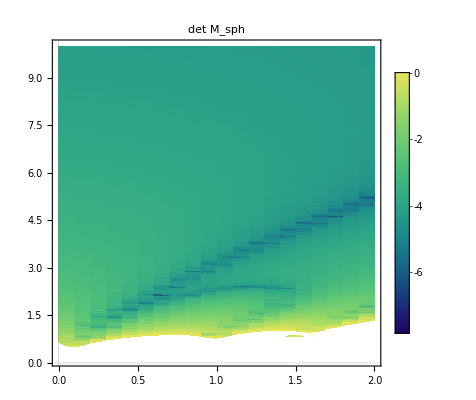

```mathematica
ListDensityPlot[matrixDeterminantValues2,PlotTheme->"Scientific",PlotLabel->"det M_sph",ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,InterpolationOrder->4]
```

```mathematica
matrixDeterminantValues=Table[{m,kmn,Log10[Abs[matrixMdeterminent[m,1.0,1.01,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]]},{kmn,1.0,1000.0,1.0},{m,0.0,2.0,0.1}]//AbsoluteTiming
matrixDeterminantValues2=ArrayFlatten[matrixDeterminantValues[[2]],1];
```

{39.1784,{{{0.,1.,-1.08566},{0.1,1.,-1.69718},{0.2,1.,-2.26903},{0.3,1.,-1.85436},{0.4,1.,-1.10843},{0.5,1.,-0.755658},{0.6,1.,-0.54578},{0.7,1.,-0.429039},6,{1.4,1.,0.143448},{1.5,1.,0.0269966},{1.6,1.,-0.409126},{1.7,1.,0.578478},{1.8,1.,1.01227},{1.9,1.,1.33168},{2.,1.,1.59575}},998,{1}}}
 |  |  |  |

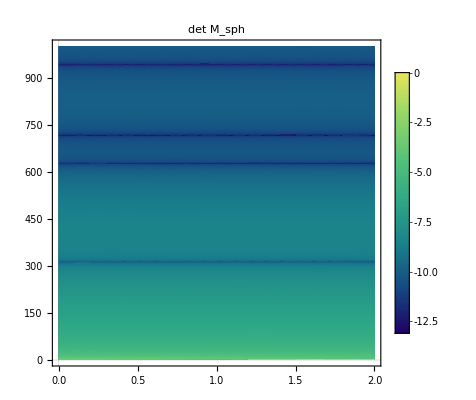

```mathematica
ListDensityPlot[matrixDeterminantValues2,PlotTheme->"Scientific",PlotLabel->"det M_sph",ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,InterpolationOrder->4]
```

```mathematica
logDeterminantValuesM1=Table[{kmn,Log10[Abs[matrixMdeterminent[1,1.0,1.1,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]]},{kmn,0.01,3.0,0.01}];
logDeterminantValuesM2=Table[{kmn,Log10[Abs[matrixMdeterminent[2,1.0,1.1,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]]},{kmn,0.01,3.0,0.01}];
```

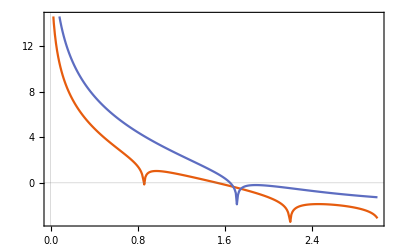

```mathematica
zerosPlot=ListPlot[{logDeterminantValuesM1,logDeterminantValuesM2},PlotTheme->"Scientific",FrameLabel->{"m","Log(det(|M|))"},Joined->True]
```

### Write down the mechanical modes for a spherical shell

```mathematica
(* define the necessary differential operators *)
rCrossNabla[myFnc_,r_,θ_,ϕ_,m_,n_,l_,a_]:={0, -(1/Sin[θ])*D[myFnc[m,n,l,a,r,θ,ϕ],ϕ], D[myFnc[m,n,l,a,r,θ,ϕ],θ]}
nablaCrossRCrossNabla[myFnc_,r_,θ_,ϕ_,m_,n_,l_,a_]:={(1/r)* D[myFnc[m,n,l,a,r,θ,ϕ],θ,θ] + (1/(r*Sin[θ]^2))*D[myFnc[m,n,l,a,r,θ,ϕ],ϕ,ϕ], -D[myFnc[m,n,l,a,r,θ,ϕ],θ,r]+(1/r)*D[myFnc[m,n,l,a,r,θ,ϕ],θ], -(1/Sin[θ])*D[myFnc[m,n,l,a,r,θ,ϕ],ϕ,r]+(1/(r*Sin[θ]))*D[myFnc[m,n,l,a,r,θ,ϕ],ϕ]}

(* mechanical frequencies *)
vt = (matieralDensity/shearModulus)^(-1/2);
vl = (matieralDensity/(lambdaMaterial+2*shearModulus))^(-1/2);
(* wave numbers *)
wavek[m_,n_,l_,a_]:=Inactivate[waveNumbersK[[m+1,n+1]]]
wavep[m_,n_,l_,a_]:=Inactivate[waveNumbersP[[m+1,n+1]]]
omegaMech[m_,n_,l_,a_]:=vt*Sqrt[wavek[m,n,l,a]]
(* constituent functions *)
auxϕ[m_,n_,l_,a_,r_,θ_,ϕ_]:=SphericalBesselJ[m,wavep[m,n,l,a]*r]*SphericalHarmonicY[m,l,θ,ϕ];
auxϕT[m_,n_,l_,a_,r_,θ_,ϕ_]:=SphericalBesselY[m,wavep[m,n,l,a]*r]*SphericalHarmonicY[m,l,θ,ϕ];
auxψ[m_,n_,l_,a_,r_,θ_,ϕ_]:=SphericalBesselJ[m,wavek[m,n,l,a]*r]*SphericalHarmonicY[m,l,θ,ϕ];
auxψT[m_,n_,l_,a_,r_,θ_,ϕ_]:=SphericalBesselY[m,wavek[m,n,l,a]*r]*SphericalHarmonicY[m,l,θ,ϕ];
(* mechanical mode displacement vector *)
garbageVariableUsedToDefineFunctions=c0*(Grad[auxϕ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"] + (d0/c0)*Grad[auxϕT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]+I*(c2/c0)*nablaCrossRCrossNabla[auxψ,r,θ,ϕ,m,n,l,a]+I*(d2/c0)*nablaCrossRCrossNabla[auxψT,r,θ,ϕ,m,n,l,a]);
displacementVecQ[m_,n_,l_,a_,c0_,d0_,c2_,d2_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=(Grad[auxϕ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"] + (d0ratio)*Grad[auxϕT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]+I*(c2ratio)*nablaCrossRCrossNabla[auxψ,r,θ,ϕ,m,n,l,a]+I*(d2ratio)*nablaCrossRCrossNabla[auxψT,r,θ,ϕ,m,n,l,a]);
displacementVecQnorm[m_,n_,l_,a_,d0ratio_,c2ratio_,d2ratio_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

### Solve for q Coefficients of Spheroidal Modes

This becomes an eigenvector problem. We take the matrix “bigMatrix” with all the appropriate parameters and solve the system of equations.

```mathematica
findCoefRatios[m_,n_]:=ArrayFlatten[LinearSolve[bigMmatrix[m,n,innerRadius,outerRadius,innerRadius,(waveNumbersK[[m+1]][[n+1]])*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],waveNumbersK[[m+1]][[n+1]]][[1;;4,2;;4]],-bigMmatrix[m,n,innerRadius,outerRadius,innerRadius,(waveNumbersK[[m+1]][[n+1]])*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],waveNumbersK[[m+1]][[n+1]]][[1;;4,1;;1]]],1]
findNormalization[m_,n_,l_]:=(NIntegrate[r^2*Sin[θ]*Norm[displacementVecQnorm[m,n,l,innerRadius,findCoefRatios[[2]],findCoefRatios[[1]],findCoefRatios[[3]],r,θ,ϕ]]^2,{r,0.0,innerRadius},{θ,0.0,Pi},{ϕ,0.0,2.0*Pi}])^(-1/2)
```

```mathematica
modeInfoDataStructure={};
For[m=2,m<3,m++,For[n=0,n<6,n++,For[l=0,l<=n,l++,ratios=findCoefRatios[m,n];c0=Quiet[(Quiet[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios[[2]],ratios[[1]],ratios[[3]],r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,Pi},{ϕ,0.01,2.0*Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]]/((4/3)*Pi*outerRadius^3 - (4/3)*Pi*innerRadius^3))^(-1/2)];modeInfoDataStructure=Append[modeInfoDataStructure,makeModeVariable[m,n,l,resonantFrequencies[[m+1,n+1]],waveNumbersK[[m+1,n+1]],waveNumbersP[[m+1,n+1]],c0,ratios[[2]]*c0,ratios[[1]]*c0,ratios[[3]]*c0]]]]]
```

```mathematica
modeInfoDataStructure
```

{m2n0l0→{wavenumberk→1.78981,wavenumberp→0.783212,frequency→2817.12,C0→26.53,C2→0.000883808,D0→1.70551,D2→-0.020327},m2n1l0→{wavenumberk→5.2182,wavenumberp→2.28346,frequency→4810.18,C0→4.25263,C2→1.41689,D0→-0.704751,D2→1.08461},m2n1l1→{wavenumberk→5.2182,wavenumberp→2.28346,frequency→4810.18,C0→4.13155,C2→1.37655,D0→-0.684684,D2→1.05372},m2n2l0→{wavenumberk→314.172,wavenumberp→137.48,frequency→37323.7,C0→0.000198884,C2→-0.000132043,D0→-0.0519556,D2→2.06776},m2n2l1→{wavenumberk→314.172,wavenumberp→137.48,frequency→37323.7,C0→0.00019861,C2→-0.000131861,D0→-0.051884,D2→2.0649},m2n2l2→{wavenumberk→314.172,wavenumberp→137.48,frequency→37323.7,C0→0.000121237,C2→-0.0000803137,D0→-0.0317377,D2→1.26139},m2n3l0→{wavenumberk→628.325,wavenumberp→274.952,frequency→52782.9,C0→0.000121491,C2→0.000150496,D0→-0.0262426,D2→2.0681},m2n3l1→{wavenumberk→628.325,wavenumberp→274.952,frequency→52782.9,C0→0.000120614,C2→0.00014941,D0→-0.0260532,D2→2.05318},m2n3l2→{wavenumberk→628.325,wavenumberp→274.952,frequency→52782.9,C0→4.31643,C2→5.3597,D0→-933.671,D2→73795.1},m2n3l3→{wavenumberk→628.325,wavenumberp→274.952,frequency→52782.9,C0→4.31864,C2→5.33703,D0→-943.132,D2→74450.8},m2n4l0→{wavenumberk→717.946,wavenumberp→314.17,frequency→56421.9,C0→4.32348,C2→-2.56019,D0→0.0232301,D2→0.0141897},m2n4l1→{wavenumberk→717.946,wavenumberp→314.17,frequency→56421.9,C0→4.3764,C2→-2.59153,D0→0.0235145,D2→0.0143634},m2n4l2→{wavenumberk→717.946,wavenumberp→314.17,frequency→56421.9,C0→0.0000135938,C2→-8.05919×10^-6,D0→7.30324×10^-8,D2→4.4344×10^-8},m2n4l3→{wavenumberk→717.946,wavenumberp→314.17,frequency→56421.9,C0→0.0000136819,C2→-8.03572×10^-6,D0→7.33153×10^-8,D2→4.46278×10^-8},m2n4l4→{wavenumberk→717.946,wavenumberp→314.17,frequency→56421.9,C0→0.0000135877,C2→-8.04714×10^-6,D0→7.30215×10^-8,D2→4.46164×10^-8},m2n5l0→{wavenumberk→942.482,wavenumberp→412.425,frequency→64645.4,C0→0.0000134625,C2→-0.0000130256,D0→-0.0172264,D2→2.04236},m2n5l1→{wavenumberk→942.482,wavenumberp→412.425,frequency→64645.4,C0→0.0000135296,C2→-0.0000130906,D0→-0.0173124,D2→2.05255},m2n5l2→{wavenumberk→942.482,wavenumberp→412.425,frequency→64645.4,C0→0.356265/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5]),C2→-(0.344705/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])),D0→-(455.872/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])),D2→54048./(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])},m2n5l3→{wavenumberk→942.482,wavenumberp→412.425,frequency→64645.4,C0→0.356265/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5]),C2→-(0.344705/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])),D0→-(455.872/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])),D2→54048./(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])},m2n5l4→{wavenumberk→942.482,wavenumberp→412.425,frequency→64645.4,C0→0.356265/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5]),C2→-(0.344705/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])),D0→-(455.872/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])),D2→54048./(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])},m2n5l5→{wavenumberk→942.482,wavenumberp→412.425,frequency→64645.4,C0→0.356265/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5]),C2→-(0.344705/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])),D0→-(455.872/(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])),D2→54048./(√NIntegrate[Activate[r^2 Sin[θ] Quiet[Norm[Quiet[displacementVecQnorm[m,n,l,innerRadius,ratios⟦2⟧,ratios⟦1⟧,ratios⟦3⟧,r,θ,ϕ]]]]^2],{r,innerRadius,outerRadius},{θ,0.01,π},{ϕ,0.01,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5])}}

```mathematica
Quiet[Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/radius1-thickness1percent/NbCavity-r=1.0-1.01.txt",InputForm[modeInfoDataStructure]]]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/radius1-thickness1percent/NbCavity-r=1.0-1.01.txt

```mathematica
MODES =Quiet[ToExpression[Quiet[Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/radius1-thickness1percent/NbCavity-r=1.0-1.01.txt"]]]];
```

```mathematica
"C2"/.("m2n0l0"/.MODES[[1]])
```

0.000883808